```mathematica
Get["new1through5Sequential.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward10[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Get["new1through5Sequential_20Kimura.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward20[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Get["new1through5Sequential_30Kimura.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward30[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG, expectation, soln];
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.01;
VG =.000101;
expectation = 0.1;
```

```mathematica
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,0.2},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.05}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg10_gen50.png",%24,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg10_gen50.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.1}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg10_gen100.png",%29,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg10_gen100.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.15}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg10_gen150.png",%34,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg10_gen150.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.05}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg20_gen50.png",%39,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg20_gen50.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.1}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg20_gen100.png",%44,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg20_gen100.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.15}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg20_gen150.png",%49,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg20_gen150.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.05}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg30_gen50.png",%54,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg30_gen50.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.1}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg30_gen100.png",%59,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg30_gen100.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.15}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg30_gen150.png",%64,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg30_gen150.png

```mathematica
(***************************************************************************************************************************)
```

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG, expectation, soln];
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.005;
VG =.000101;
expectation = 0.1;
```

```mathematica
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,1},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.25}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg10_gen250.png",%89,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg10_gen250.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.5}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg10_gen500.png",%94,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg10_gen500.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.75}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg10_gen750.png",%99,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg10_gen750.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.25}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg20_gen250.png",%104,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg20_gen250.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.5}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg20_gen500.png",%109,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg20_gen500.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.75}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg20_gen750.png",%114,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg20_gen750.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.25}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg30_gen250.png",%119,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg30_gen250.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.5}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg30_gen500.png",%124,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg30_gen500.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.75}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg30_gen750.png",%129,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg30_gen750.png

```mathematica
(******************************************************************************************************)
```

```mathematica
Clear[new]
```

```mathematica
Get["new1through5Sequential_50Kimura.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward50[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG, expectation, soln];
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.001;
VG =.000101;
expectation = 0.1;
```

```mathematica
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,0.05},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na1_geg10_gen20.png",%158,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na1_geg10_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na1_geg30_gen20.png",%162,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na1_geg30_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward50[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward50[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na1_geg50_gen20.png",%166,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na1_geg50_gen20.png

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG, expectation, soln];
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.005;
VG =.000101;
expectation = 0.1;
```

```mathematica
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,0.05},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg10_gen20.png",%182,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg10_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg30_gen20.png",%186,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg30_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward50[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward50[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg50_gen20.png",%190,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg50_gen20.png

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG, expectation, soln];
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.01;
VG =.000101;
expectation = 0.1;
```

```mathematica
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,0.05},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg10_gen20.png",%206,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg10_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg30_gen20.png",%210,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg30_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward50[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward50[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg50_gen20.png",%214,"PNG"]
```

```mathematica
"C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg50_gen20.png"
```

```mathematica
(******************************************************************************************************)
```

```mathematica
Clear[new]
```

```mathematica
Get["new1through5Sequential_50Kimura.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward50[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
neutral = Kimura[x,y,t,50];
```

```mathematica
Clear[out];
out = {{"alpha","VG","start","thresh","totalP","Pdetected","Pnotdetected
"}};
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
time = 0.05;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
out
```

{{alpha,VG,start,thresh,totalP,Pdetected,Pnotdetected
}}

```mathematica
α = 0.01
VG = 0.00101
```

0.01

0.00101

0.1

print[0.1]

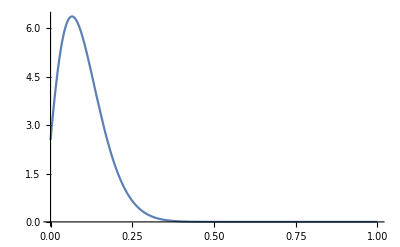

```mathematica
expectation = 0.1
print[expectation]
Plot[neutral/. {x->expectation, t->time}, {y,0,1}]
```

```mathematica
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}]
pNeutFix = 1- neutAUC
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}]
thresh = Solve[tmp == (sigCutoff - pNeutFix) && 0<Ψ<1, {Ψ}, Reals]
Print[thresh]
If[Length[thresh] != 1,Throw[{α, VG, thresh}]]
Ψ = Ψ /. thresh
Print[Ψ]
```

$Aborted

```mathematica
Plot[Evaluate[Table[SimplifiedHayward50[k]/. {x->expectation,t ->time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,5}]}]
FindMinimum[Evaluate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar,VG->genVar}],{y,0,1}]
totalP = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, 0,1}]
Pdetectedplus = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Min[expectation+Ψ,1],1}]
Pnotdetected = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

```mathematica
Do[Clear[expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected];
expectation = start;
print[expectation];
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}];
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}];
thresh = Solve[tmp == (sigCutoff - pNeutFix) && 0<Ψ<1, {Ψ}, Reals];
Print[thresh];
If[Length[thresh] != 1,Throw[{α, VG, thresh}]];
Ψ = Ψ /. thresh;
Print[Ψ];
totalP = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, 0,1}];
Pdetectedplus = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Min[expectation+Ψ,1],1}];
Pnotdetected = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}];
AppendTo[out,{α,VG,expectation,Ψ[[1]],totalP,Pdetected,Pnotdetected}],
{α, {0.00025, 0.0005, 0.00075,0.001,0.002,0.005, 0.01}},
{VG, {.101, .0101, .00101,.000101}}
]
out
Export["alpha_VG.csv",out,"csv"];
```